Dynamic simulation of three-wheeled omnidirectional mobile robot

```mathematica
Clear["Global`*"];
```

## Section I.

### Configuration definition

#### Global coordinate system definition

```mathematica
ux={1,0,0};
uy={0,1,0};
uz={0,0,1};
rO={0,0,0};
```

#### Basic coordinate system definition

```mathematica
φA=π/6; φB=φA+(2π)/3;φC=φB+(2π)/3;
```

```mathematica
uxA=RotationMatrix[φA,{0,0,1}].ux;
uxB=RotationMatrix[φB,{0,0,1}].ux;
uxC=RotationMatrix[φC,{0,0,1}].ux;
uyA=RotationMatrix[φA,{0,0,1}].uy;
uyB=RotationMatrix[φB,{0,0,1}].uy;
uyC=RotationMatrix[φC,{0,0,1}].uy;
uzA=Cross[uxA,uyA];
uzB=Cross[uxB,uyB];
uzC=Cross[uxC,uyC];
```

### Geometry parameters

#### Wheel definition

```mathematica
wheelCircleRadius=0.12;
wheelRadius=0.03;
wheelWidth=0.020;
massWheel=0.06;
A=({{-Sin[φA], Cos[φA], wheelCircleRadius}, {-Sin[φB], Cos[φB], wheelCircleRadius}, {-Sin[φC], Cos[φC], wheelCircleRadius}});
```

```mathematica
rA=wheelCircleRadius uxA;
rB=wheelCircleRadius uxB;
rC=wheelCircleRadius uxC;
wheelθMeasured = 0.0390;
```

#### Case definition

```mathematica
ρ=7850;
dummyCaseRadius=0.8 wheelCircleRadius;
dummyCaseHeight=0.008;
rSCase={0,0,dummyCaseHeight/2};
mCase=dummyCaseRadius^2 π dummyCaseHeight ρ
```

1.81824

#### Package definition

```mathematica
packageHeight = 0.50;
packageRadius=0.3 dummyCaseRadius;
rSPackage={0,0,dummyCaseHeight/2+packageHeight/2};
mPackage=packageRadius^2 π packageHeight ρ
```

10.2276

#### Common mass center

```mathematica
rS=rSCase;
rS=(rSCase mCase+rSPackage mPackage)/(mCase+mPackage)
```

{0.,0.,0.216264}

### 3 D model of the robot and its environment

#### Draw functions

```mathematica
TranslateAndRotate[g_,x_,y_,α_]:=Module[{},Rotate[Translate[g,{x,y}],α,{x,y}]]
```

```mathematica
RobotCaseGraphics3D={
Red,Sphere[rO,wheelCircleRadius/100],
Pink,Opacity[0.8],
Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rB-wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rC-wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0})},wheelRadius],
Gray,Thick,Opacity[1],
	Line[{0.8 rA,rA}],
	Line[{0.8 rB,rB}],
	Line[{0.8 rC,rC}],
Cyan,Opacity[0.6],
Cylinder[{rO-dummyCaseHeight/2 uz,rSCase+dummyCaseHeight/2 uz},dummyCaseRadius],
Black,Opacity[0.6],EdgeForm[White],
Cylinder[{rSCase+dummyCaseHeight/2 uz,rSCase+dummyCaseHeight/2 uz+packageHeight uz},packageRadius]
};
```

```mathematica
DrawRobot3D[{x_,y_,z_,α_}]:={EdgeForm[Black],Rotate[Translate[RobotCaseGraphics3D,{x,y,z}],α,{0,0,1}]}
```

```mathematica
DrawGround={EdgeForm[Black],
planeSize=60 wheelCircleRadius;
Gray,Yellow,Polygon[{{-planeSize wheelCircleRadius,-planeSize wheelCircleRadius,-wheelRadius},{-planeSize wheelCircleRadius,planeSize wheelCircleRadius,-wheelRadius},{planeSize wheelCircleRadius,planeSize wheelCircleRadius,-wheelRadius},{planeSize wheelCircleRadius,-planeSize  wheelCircleRadius,-wheelRadius}}]
};
```

```mathematica
DrawGlobalAxes[{x_,y_,z_,φ_}]:={EdgeForm[Black],
Translate[
{
Gray,
	Line[{rO,ux planeSize/13}],Text["x",1.2ux planeSize/13],
	Line[{rO,uy planeSize/13}],Text["y",1.2uy planeSize/13],
	Line[{rO,uz planeSize/13}],Text["z",1.2uz planeSize/13],

},{x,y,z}]}
```

#### Draw 3D graphics

```mathematica
DrawRobot3D[{0,0,0,π/9}]//Graphics3D
```

-Graphics3D-

```mathematica
initialPos={0,0,0,0};
Graphics3D[
DrawRobot3D[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround,
AxesLabel->{x,y,z},Axes->{True, True, True}]
```

-Graphics3D-

### Free Body Diagrams

#### Draw functions

```mathematica
aM=wheelCircleRadius;
vM=0.4 wheelCircleRadius;
vThick=vM/12;
vArrHead=0.6 vM;
DrawCaseFBD={
Red,Sphere[rO,wheelCircleRadius/100],
Gray,
	Line[{rO,1.5ux aM}],Text[x,1.6ux aM],
	Line[{rO,1.5uy aM}],Text[y,1.6uy aM],
	Line[{rO,1.5uz aM}],Text[z,1.6uz aM],
Black,Thick,
	Line[{rO,rA}],
	Line[{rO,rB}],
	Line[{rO,rC}],
Blue,Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rO,rO-vM uz}],Text["G",1.2(rO-vM uz)],
	Arrow[{rA,rA+vM ux}],Text["K_x^A",1.1(rA+vM ux)],
	Arrow[{rA,rA+vM uy}],Text["K_y^A",1.1(rA+vM uy)],
	Arrow[{rA,rA+vM uz}],Text["K_z^A",1.1(rA+vM uz)],
	Arrow[{rB,rB+vM ux}],Text["K_x^B",1.1(rB+vM ux)],
	Arrow[{rB,rB+vM uy}],Text["K_y^B",1.1(rB+vM uy)],
	Arrow[{rB,rB+vM uz}],Text["K_z^B",1.1(rB+vM uz)],
	Arrow[{rC,rC+vM ux}],Text["K_x^C",1.1(rC+vM ux)],
	Arrow[{rC,rC+vM uy}],Text["K_y^C",1.1(rC+vM uy)],
	Arrow[{rC,rC+vM uz}],Text["K_z^C",1.1(rC+vM uz)],
Red,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rO,1.4(rO+vM ux)}],Text["ϵ_x",1.6(rO+vM ux)],
	Arrow[{rO,1.4(rO+vM uy)}],Text["ϵ_y",1.6(rO+vM uy)],
	Arrow[{rO,1.4(rO+vM uz)}],Text["ϵ_z",1.6(rO+vM uz)],
Thickness[1.2 vThick],Arrowheads[1.2 vArrHead],
	Arrow[{rO,rO+vM ux}],Text["a_x",1.1(rO+vM ux)],
	Arrow[{rO,rO+vM uy}],Text["a_y",1.1(rO+vM uy)],
	Arrow[{rO,rO+vM uz}],Text["a_z",1.1(rO+vM uz)],
};
DrawAccelerationState[ax_,ay_,ϵz_,MA_,MB_,MC_,nA_,nB_,nC_]:={
M1=wheelCircleRadius;
M2=20 wheelCircleRadius;
accv=M1 {ax,ay,ϵz/20};
axy=N[√(ax^2+ay^2)];
Mv=-M2 {MA,MB,MC};
Red,Sphere[rO,wheelCircleRadius/100],
Blue,Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA+Mv⟦1⟧ uyA}],Text["M_A="<>ToString[NumberForm[MA,{6,2}]]<>"[Nm]"<>"\n"<>"n_A="<>ToString[NumberForm[nA,{6,2}]]<>"[N]",rA+4 vM uxA],
	Arrow[{rB,rB+Mv⟦2⟧  uyB}],Text["M_B="<>ToString[NumberForm[MB,{6,2}]]<>"[Nm]"<>"\n"<>"n_B="<>ToString[NumberForm[nB,{6,2}]]<>"[N]",rB+4vM uxB],
	Arrow[{rC,rC+Mv⟦3⟧  uyC}],Text["M_C="<>ToString[NumberForm[MC,{6,2}]]<>"[Nm]"<>"\n"<>"n_C="<>ToString[NumberForm[nC,{6,2}]]<>"[N]",rC+4vM uxC],
Red,
Thickness[vThick],Arrowheads[vArrHead],
	If[ϵz≠0,{Arrow[{rO,rO+ accv⟦3⟧ uz}],Text["ϵ_z="<>ToString[NumberForm[ϵz,{6,2}]]<>"[s^-2]",1.2(rO+ accv⟦3⟧ uz)]},],
Thickness[vThick],Arrowheads[1.2 vArrHead],
	(*If[ax≠0,{Arrow[{rO,rO+ accv⟦1⟧ ux}],Text["a_x="<>ToString[ax]<>"[m s^-2]",1.2(rO+ accv⟦1⟧ ux)]},],
	If[ay≠0,{Arrow[{rO,rO+ accv⟦2⟧ uy}],Text["a_y="<>ToString[ay]<>"[m s^-2]",1.2(rO+ accv⟦2⟧ uy)]},],*)
If[ay≠0||ax≠0,{Arrow[{rS,rS+ accv⟦2⟧ uy+ accv⟦1⟧ ux}],Text["a_xy="<>ToString[NumberForm[axy,{6,2}]]<>"[m s^-2]",1.2(rS+ accv⟦2⟧ uy+ accv⟦1⟧ ux)]},],
};
```

```mathematica
aM=0.15;
vM=0.06;
vThick=vM/30;
vArrHead=0.2 vM;
DrawWheelsFBD={
Red,Sphere[rA,wheelCircleRadius/50],
Gray,
	Line[{rA,rA+uxA aM}],Text["x_A",1.1(rA+uxA aM)],
	Line[{rA,rA+uyA aM}],Text["y_A",1.1(rA+uyA aM)],
	Line[{rA,rA+uzA aM}],Text["z_A",1.1(rA+uzA aM)],
	Line[{rB,rB+uxB aM}],Text["x_B",1.1(rB+uxB aM)],
	Line[{rB,rB+uyB aM}],Text["y_B",1.1(rB+uyB aM)],
	Line[{rB,rB+uzB aM}],Text["z_B",1.1(rB+uzB aM)],
	Line[{rC,rC+uxC aM}],Text["x_C",1.1(rC+uxC aM)],
	Line[{rC,rC+uyC aM}],Text["y_C",1.1(rC+uyC aM)],
	Line[{rC,rC+uzC aM}],Text["z_C",1.1(rC+uzC aM)],
Red,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA+1.5vM uxA}],Text["ϵ_x^A",rA+1.7vM uxA],
	Arrow[{rA,rA+1.5vM uyA}],Text["ϵ_y^A",rA+1.7vM uyA],
	Arrow[{rA,rA+1.5vM uzA}],Text["ϵ_z^A",rA+1.7vM uzA],
	Arrow[{rB,rB+1.5vM uxB}],Text["ϵ_x^B",rB+1.7vM uxB],
	Arrow[{rB,rB+1.5vM uyB}],Text["ϵ_y^B",rB+1.7vM uyB],
	Arrow[{rB,rB+1.5vM uzB}],Text["ϵ_z^B",rB+1.7vM uzB],
	Arrow[{rC,rC+1.5vM uxC}],Text["ϵ_x^C",rC+1.7vM uxC],
	Arrow[{rC,rC+1.5vM uyC}],Text["ϵ_y^C",rC+1.7vM uyC],
	Arrow[{rC,rC+1.5vM uzC}],Text["ϵ_z^C",rC+1.7vM uzC],
Thickness[1.2 vThick],Arrowheads[1.2 vArrHead],
	Arrow[{rA,rA+2vM uxA}],Text["a_x^A",rA+2.2vM uxA],
	Arrow[{rA,rA+2vM uyA}],Text["a_y^A",rA+2.2vM uyA],
	Arrow[{rA,rA+2vM uzA}],Text["a_z^A",rA+2.2vM uzA],
Blue,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA-1.5vM uz}],Text["G_A",1.1(rA-1.5vM uz)],
	Arrow[{rB,rB-1.5vM uz}],Text["G_B",1.1(rB-1.5vM uz)],
	Arrow[{rC,rC-1.5vM uz}],Text["G_C",1.1(rC-1.5vM uz)],
	Arrow[{rA-{0,0,wheelRadius},rA-{0,0,wheelRadius}+vM uyA}],Text["S_A",1.1(rA-{0,0,wheelRadius}+vM uyA)],
	Arrow[{rB-{0,0,wheelRadius},rB-{0,0,wheelRadius}+vM uyB}],Text["S_B",1.1(rB-{0,0,wheelRadius}+vM uyB)],
	Arrow[{rC-{0,0,wheelRadius},rC-{0,0,wheelRadius}+vM uyC}],Text["S_C",1.1(rC-{0,0,wheelRadius}+vM uyC)],
	Arrow[{rA,rA-vM uxA}],Text["K_x^A",1.1(rA-vM uxA)],
	Arrow[{rA,rA-vM uyA}],Text["K_y^A",1.1(rA-vM uyA)],
	Arrow[{rA,rA-vM uzA}],Text["K_z^A",1.1(rA-vM uzA)],
	Arrow[{rB,rB-vM uxB}],Text["K_x^B",1.1(rB-vM uxB)],
	Arrow[{rB,rB-vM uyB}],Text["K_y^B",1.1(rB-vM uyB)],
	Arrow[{rB,rB-vM uzB}],Text["K_z^B",1.1(rB-vM uzB)],
	Arrow[{rC,rC-vM uxC}],Text["K_x^C",1.1(rC-vM uxC)],
	Arrow[{rC,rC-vM uyC}],Text["K_y^C",1.1(rC-vM uyC)],
	Arrow[{rC,rC-vM uzC}],Text["K_z^C",1.1(rC-vM uzC)],
Blue,Opacity[0.3],
Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rB-wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rC-wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0})},wheelRadius],
};
```

#### Draw FBDs

```mathematica
Row[{Graphics3D[DrawCaseFBD,Boxed->False,ImageSize->Large],Graphics3D[DrawWheelsFBD,Boxed->False,ImageSize->Large]}]
```

-Graphics3D--Graphics3D-

### Applying Newton’s 2nd Law

#### Case

```mathematica
a={ax,ay,az};ϵ={ϵx,ϵy,ϵz};v={vx,vy,vz};ω={ωx,ωy,ωz};
KA={KAx,KAy,KAz};KB={KBx,KBy,KBz};KC={KCx,KCy,KCz};
G={0,0,-mRobot g};
```

```mathematica
{xCS,yCS,zCS}=rS-rSCase;
{xPS,yPS,zPS}=rS-rSPackage;
```

```mathematica
θCase=({{1/4 mCase dummyCaseRadius^2+1/12 mCase dummyCaseHeight^2, 0, 0}, {0, 1/4 mCase dummyCaseRadius^2+1/12 mCase dummyCaseHeight^2, 0}, {0, 0, 1/2 mCase dummyCaseRadius^2}})+mCase ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
θPackage=({{1/4 mPackage dummyCaseRadius^2+1/12 mPackage dummyCaseHeight^2, 0, 0}, {0, 1/4 mPackage dummyCaseRadius^2+1/12 mPackage dummyCaseHeight^2, 0}, {0, 0, 1/2 mPackage dummyCaseRadius^2}})+mPackage  ({{yPS^2+zPS^2, -xPS yPS, -xPS zPS}, {-yPS xPS, xPS^2+zPS^2, -yPS zPS}, {-zPS xPS, -zPS yPS, xPS^2+yPS^2}});
```

```mathematica
eq1=mRobot a== KA+KB+KC+G
```

{ax mRobot,ay mRobot,az mRobot}=={KAx+KBx+KCx,KAy+KBy+KCy,KAz+KBz+KCz-g mRobot}

```mathematica
eq2=θRobot. ϵ+Cross[ω,θRobot.ω]==Cross[rA-rS,KA]+Cross[rB-rS,KB]+Cross[rC-rS,KC]
```

{ωx,ωy,ωz}×(θRobot.{ωx,ωy,ωz})+θRobot.{ϵx,ϵy,ϵz}=={0.216264 KAy+0.06 KAz+0.216264 KBy+0.06 KBz+0.216264 KCy-0.12 KCz,0.-0.216264 KAx-0.103923 KAz-0.216264 KBx+0.103923 KBz-0.216264 KCx,0.-0.06 KAx+0.103923 KAy-0.06 KBx-0.103923 KBy+0.12 KCx}

#### Wheels

```mathematica
KAA=-RotationMatrix[-φA,{0,0,1}].KA;
KBB=-RotationMatrix[-φB,{0,0,1}].KB;
KCC=-RotationMatrix[-φC,{0,0,1}].KC;
```

```mathematica
aA={aAx,aAy,aAz};ϵA={ϵAx,ϵAy,ϵAz};vA={vAx,vAy,vAz};ωA={ωAx,ωAy,ωAz};
aB={aBx,aBy,aBz};ϵB={ϵBx,ϵBy,ϵBz};vB={vBx,vBy,vBz};ωB={ωBx,ωBy,ωBz};
aC={aCx,aCy,aCz};ϵC={ϵCx,ϵCy,ϵCz};vA={vCx,vCy,vCz};ωC={ωCx,ωCy,ωCz};
G={0,0,-mWheel g};
SA=sA {0,1,0};SB=sB {0,1,0};SC=sC {0,1,0};NA=nA {0,0,1};NB=nB {0,0,1};NC=nC {0,0,1};
```

```mathematica
θWheel=({{1/4 mWheel wheelRadius^2+1/12 mWheel wheelWidth^2, 0, 0}, {0, 1/4 mWheel wheelRadius^2+1/12 mWheel wheelWidth^2, 0}, {0, 0, 1/2 mWheel wheelRadius^2}});
```

```mathematica
θWheel=({{wheelθMeasured, 0, 0}, {0, wheelθMeasured, 0}, {0, 0, wheelθMeasured}});
```

```mathematica
eq1A=mWheel aA== KAA+SA+G+NA;
eq1B=mWheel aB== KBB+SB+G+NB;
eq1C=mWheel aC== KCC+SC+G+NC;
```

```mathematica
eq2A=θWheel. ϵA+Cross[ωA,θWheel.ωA]=={MA,0,0}+Cross[-{0,0,wheelRadius},SA]
eq2B=θWheel. ϵB+Cross[ωB,θWheel.ωB]=={MB,0,0}+Cross[-{0,0,wheelRadius},SB];
eq2C=θWheel. ϵC+Cross[ωC,θWheel.ωC]=={MC,0,0}+Cross[-{0,0,wheelRadius},SC];
```

{0.+0.039 ϵAx,0.+0.039 ϵAy,0.+0.039 ϵAz}=={MA+0.03 sA,0.,0}

#### Constraints

2D rolling

```mathematica
(*No slip condition in yWheel direction*)
rollingY={aAy,aBy,aCy}==-wheelRadius{ϵAx,ϵBx,ϵCx};
(*Contact condition in zWheel direction*)
rollingZ={aAz,aBz,aCz}=={0,0,0}; 
(*Car - 2D motion*)
```

Rigid body connection between wheels and the case

```mathematica
kA=aA==RotationMatrix[-φA,{0,0,1}].(a+Cross[ϵ,rA]+Cross[ω,Cross[ω,rA]]);
kB=aB==RotationMatrix[-φB,{0,0,1}].(a+Cross[ϵ,rB]+Cross[ω,Cross[ω,rB]]);
kC=aC==RotationMatrix[-φC,{0,0,1}].(a+Cross[ϵ,rC]+Cross[ω,Cross[ω,rC]]);
```

#### Electromechanical equations

```mathematica
L=0
```

0

```mathematica
θ=0.038999801486034;
b=0.004483480554580;
K=0.998019215315511;
R=3.068968068446540;
L=0;
V=12;
TL= 0;
```

```mathematica
Clear[V]
```

```mathematica
MomentEquation = θ x'[t] +b x[t] == K y[t]-TL
KirchoffEquation = L y'[t]+R y[t] ==V-K x[t]
```

0.00448348 x[t]+0.0389998 x'[t]==0.998019 y[t]

3.06897 y[t]==V-0.998019 x[t]

```mathematica
CombinedEquation = MomentEquation/.Solve[KirchoffEquation,y[t]][[1]]//Simplify
```

1. V==1.01181 x[t]+0.119927 x'[t]

```mathematica
solution = DSolve[{CombinedEquation,x[0]==0},x[t],t]
```

{{x[t]→0.988332 ⅇ^(-8.43687 t) (-1. V+1. ⅇ^(8.43687 t) V)}}

```mathematica
RotationalSpeedAnalytic = x[t]/.solution[[1]]//Simplify
```

(0.988332-0.988332 ⅇ^(-8.43687 t)) V

```mathematica
ArmatureCurrentAnalytic = y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify
```

(0.00443996+0.321402 ⅇ^(-8.43687 t)) V

```mathematica
TorqueAnalytic = K y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify
```

(0.00443117+0.320766 ⅇ^(-8.43687 t)) V

```mathematica
VoltageToTorque[V_,t_]= K y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.DSolve[{MomentEquation/.Solve[KirchoffEquation,y[t]][[1]],x[0]==0},x[t],t][[1]]//Simplify
```

(0.00443117+0.320766 ⅇ^(-8.43687 t)) V

```mathematica
VoltageToTorque[12,0]
```

3.90236

#### Solve with numerical values

```mathematica
mRobot=mCase+mPackage;
(*Clear[mPackage,θPackage];*)θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=massWheel;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{UA,UB,UC}=12 A.{0,1,0};
{MA,MB,MC}=-{VoltageToTorque[UA,0],VoltageToTorque[UB,0],VoltageToTorque[UC,0]}
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
```

{-3.37955,3.37955,0.}

```mathematica
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions//MatrixForm//Chop
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

(ax→0
ay→2.52659
az→0
ϵx→0
ϵy→0
ϵz→0
KAx→-8.9171
KBx→8.9171
KCx→0
KAy→15.2933
KBy→15.2933
KCy→-0.151595
KAz→21.1067
KBz→21.1067
KCz→75.9566
sA→17.8342
sB→-17.8342
sC→0
nA→21.6953
nB→21.6953
nC→76.5452
aAx→1.2633
aAy→2.18809
aAz→0
aBx→1.2633
aBy→-2.18809
aBz→0
aCx→-2.52659
aCy→0
aCz→0
ϵAx→-72.9364
ϵBx→72.9364
ϵCx→0
ϵAy→0
ϵBy→0
ϵCy→0
ϵAz→0
ϵBz→0
ϵCz→0)

```mathematica
Graphics3D[
DrawRobot3D[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround~Join~DrawAccelerationState[values⟦1⟧,values⟦2⟧,values⟦3⟧,MA,MB,MC,values⟦19⟧,values⟦20⟧,values⟦21⟧],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[
Clear[MA,MB,MC];
mRobot=mCase+mPackage; θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=massWheel;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{MA,MB,MC}=-A.{aaa Cos[bbb],aaa Sin[bbb], ccc};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}]//Chop;
valuesM={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
Graphics3D[
DrawRobot3D[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround~Join~DrawAccelerationState[valuesM⟦1⟧,valuesM⟦2⟧,valuesM⟦6⟧,MA,MB,MC,valuesM⟦19⟧,valuesM⟦20⟧,valuesM⟦21⟧],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False,ImageSize->Large]
,
{{aaa,.1,"a_xy"},0,.1},
{{bbb,π/2,"φ"},0,2 π},
{{ccc,0,"ϵ_z"},0,1}]
```

```mathematica
Clear[MA,MB,MC];
mRobot=mCase+mPackage; θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=massWheel;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{MA,MB,MC}=-A.{ Cos[φ], Sin[φ],δ};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}]//Chop;
solutions//MatrixForm;
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

```mathematica
NA=values[[19]]
NB=values[[20]]
NC=values[[21]]
```

39.9786-8.11499 Cos[φ]-4.68519 Sin[φ]

39.9786+8.11499 Cos[φ]-4.68519 Sin[φ]

39.9786+9.37038 Sin[φ]

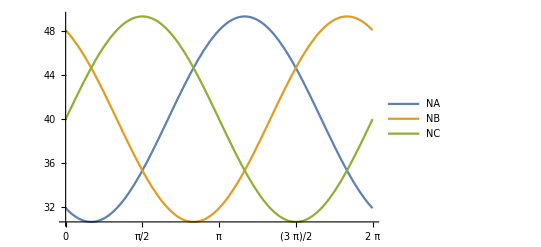

```mathematica
Plot[{NA,NB,NC},{φ,0,2 π},PlotLegends->"Expressions",Ticks->{Range[0,2 Pi,Pi/4],Automatic}]
```

Dangerous orientations

```mathematica
DA=(φ/.FindRoot[D[NA,φ]==0,{φ,π/4}]) 180/π
DB=(φ/.FindRoot[D[NB,φ]==0,{φ,3 π/4}]) 180/π
DC=(φ/.FindRoot[D[NC,φ]==0,{φ,6π/4}]) 180/π
```

30.

150.

270.